```mathematica
(*Mathematica*)
```

```mathematica
(*Bonacci 6*)
p[x_]=ExpandAll[-1-x-x^2-x^3-x^4-x^5+x^6]
```

-1-x-x^2-x^3-x^4-x^5+x^6

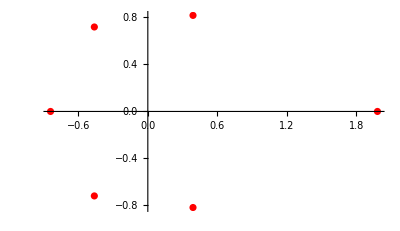

```mathematica
ComplexListPlot[z/.NSolve[p[z]==0,z],PlotStyle->Red]
```

```mathematica
ϕ=N[GoldenRatio];
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
sc=2.0;
```

```mathematica
f[z_]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)*(z^2-(sc*r[6])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1)*(-(sc*r[6]*z)^2+1))
```

-((0.737369+0.67549 ⅈ) z^12 (-15.7384+z^2) (-2.82448+z^2) ((1.21516-2.65755 ⅈ)+z^2) ((1.21516+2.65755 ⅈ)+z^2) ((2.06628-2.55364 ⅈ)+z^2) ((2.06628+2.55364 ⅈ)+z^2))/((1-15.7384 z^2) (1-2.82448 z^2) (1+(1.21516-2.65755 ⅈ) z^2) (1+(1.21516+2.65755 ⅈ) z^2) (1+(2.06628-2.55364 ⅈ) z^2) (1+(2.06628+2.55364 ⅈ) z^2))

```mathematica
g0=JuliaSetPlot[f[z],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All];
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by Roger Lee .10Bagula 18 July 2023 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nn=4,nzold=0},
	For[
		escapeCount = 0,
		(Abs[nz]<64) && (escapeCount < 2048) &&(Abs[nz-nzold]>0.5*10^(-3)),
		nzold=nz;
		nz=f[nz];
		++escapeCount
	];
	
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),escapeCount*(2*Pi-Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]]),escapeCount*(2*Pi-Arg[nz]*(Max[1-Arg[nz]/(2*Pi),Arg[nz]/(2*Pi)]))]
	
	
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.75001,2.75,1000},{-2.5001,2.75,1000}}];
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Tue 1 Jul 2025. Please

General::munfl: (-2.56667×10^-28+9.83627×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.41094×10^-32-5.72904×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.66468×10^-35-3.4089×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.75051×10^-32+1.81024×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.98656×10^-27-5.16784×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.09761×10^-29-7.1439×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.26038×10^-36-1.43683×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.53975×10^-36+3.54168×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.4352×10^-27-1.74903×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.67404×10^-36-2.2099×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.2945×10^-27+5.00972×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.29862×10^-30-9.96638×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.17082×10^-28+9.31046×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.91955×10^-36-9.60116×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.05201×10^-32-2.35062×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.15658×10^-30-2.432×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.52227×10^-27+4.43066×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.77331×10^-37-1.77499×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-4.10948×10^-31+6.72798×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.767×10^-29-2.56196×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.09381×10^-30-2.53519×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.28182×10^-29-2.86737×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.20215×10^-33-7.67201×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.28511×10^-29+1.22256×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (7.94737×10^-36+9.29712×10^-37 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.59376×10^-31+4.7008×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.05671×10^-29+7.54677×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.44024×10^-27-1.73027×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.13134×10^-27-1.26119×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.37885×10^-28-2.57631×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-5.69086×10^-30+2.05438×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.58002×10^-37-3.09964×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-9.53935×10^-29-7.37368×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.51624×10^-33+4.37285×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.25813×10^-27+2.92608×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-9.01994×10^-31+1.70788×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.03905×10^-35+8.42206×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.83729×10^-27+8.02663×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.27826×10^-27+8.76192×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-9.86955×10^-30+1.7904×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.9394×10^-36+1.75741×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.83141×10^-28-2.78028×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (5.43081×10^-29+1.09601×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.62777×10^-34-4.03217×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-9.89753×10^-32-4.90142×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-3.39727×10^-37-2.30922×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.71845×10^-29+1.36518×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.3778×10^-33-1.49483×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.80575×10^-31-2.1721×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.79639×10^-35+7.40208×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.10878×10^-36+6.13623×10^-38 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-7.39449×10^-29+1.58856×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.21543×10^-26-6.49847×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.14148×10^-28+1.67636×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.55786×10^-27-3.0363×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.91525×10^-28-2.79035×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.17439×10^-32+1.17935×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-3.25028×10^-28+1.75969×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.59269×10^-30+2.75638×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.37553×10^-32-1.63315×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (8.77977×10^-32+4.76643×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.11388×10^-36+2.76074×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.98613×10^-27+5.34667×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
g1=ListPlot3D[N[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=ListDensityPlot[arraym,   Mesh -> False,     AspectRatio -> Automatic, ColorFunction->(Hue[(2*#)]&),ImageSize->2000,Axes->False,ImageSize->2000,Frame->False];
```

```mathematica
colortab=Reverse[Union[Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/6,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/12]]]];
```

```mathematica
Length[%]
```

447

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/447,1,Ceiling[447*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=Rasterize[ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["j_1000_Bonacci6_z12_Herman_rings_3d_Inside_Outside_monitor_grid.jpg",GraphicsGrid[{{g0,g1},{g2,g3}},ImageSize->{{4000,4000}}]]
```

j_1000_Bonacci6_z12_Herman_rings_3d_Inside_Outside_monitor_grid.jpg

```mathematica
(*end*)
```